In this notebook, we study the tradeoffs between natural and adversarial error.
We use the following data model.
	• Y is sampled uniformly from {True, False}.
	• X = (X_1, X_2)
	• X_1=Y
	• X_2=Y with probability p and ¬Y with probability (1 - p).

Our threat model allows the adversary to arbitrarily perturb X_1, but the adversary cannot modify X_2
We consider randomized classifiers f from X to Y below, and as notation:
			a = P(f(0, 0) = 1), b = P(f(0, 1) = 1), c = P(f(1, 0) = 1), d = P(f(1, 1) = 1).

```mathematica
natErr[p_,a_,b_,c_,d_]:=1/2(p a+(1-p)b)+1/2((1-p)(1-c)+p (1-d))
advErr[p_,a_,b_,c_,d_]:=(
      1/2(p Max[a,c]+(1-p)Max[b,d])
+ 1/2((1-p)Max[1-a,1-c]+p Max[1-b,1-d])
)
natAdvErrs[p_,a_,b_,c_,d_]:={natErr[p,a,b,c,d],advErr[p,a,b,c,d] }
natAdvErrs[p,0,0, 1, 1]
```

{0,1}

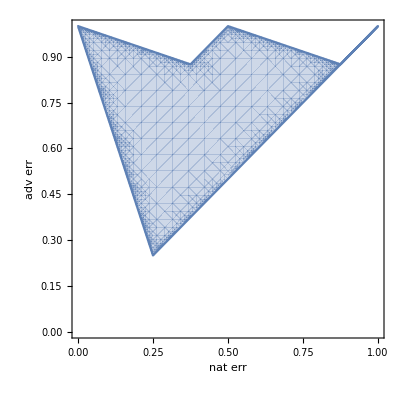

```mathematica
achievableErrs[p_]:= FunctionRange[
{
natAdvErrs[p,a,b,c,d],
0≤a≤1,0≤b≤1,0≤c≤1,0≤d≤1
},
{a,b,c,d},
{nat,adv},
Method->{"Reduced"->True}
]
accRegion=achievableErrs[3/4];
RegionPlot[
accRegion,{nat, 0, 1}, {adv, 0, 1},
PerformanceGoal->"Quality",MaxRecursion->5,
FrameLabel->{"nat err", "adv err"}
]
```